```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY207/sec_int_data/500nm.dat"]
```

{{1.65577,0.10436},{1.59352,0.11947},{1.51672,0.140023},{1.46373,0.191859},{1.42047,0.199916},{1.37769,0.218573},{1.34607,0.238859},{1.31418,0.240983},{1.27734,0.239883},{1.24989,0.218975},{1.21939,0.2599},{1.20221,0.249669},{1.18519,0.235941},{1.17023,0.245766},{1.1572,0.226578},{1.14604,0.217769},{1.13497,0.211071},{1.12762,0.176806},{1.12192,0.198441},{1.11852,0.205061},{1.11638,0.211152},{1.11532,0.199506},{1.11466,0.290503},{1.11691,0.282091},{1.12052,0.319399},{1.12514,0.329448},{1.15252,0.275356},{1.18204,0.242319},{1.20774,0.313642},{1.24068,0.320923},{1.28541,0.301363},{1.36328,0.270256},{1.4246,0.2599}}

0.482986-0.197824 x

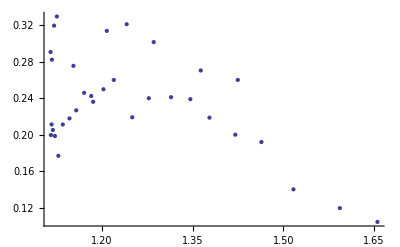

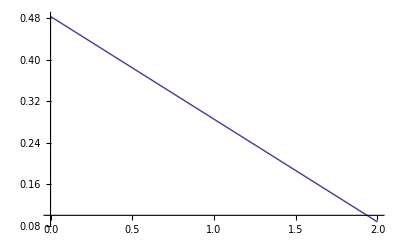

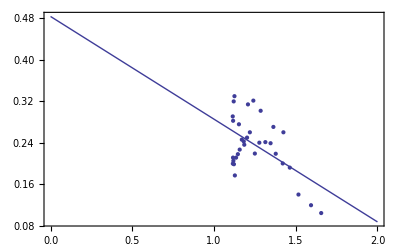

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```